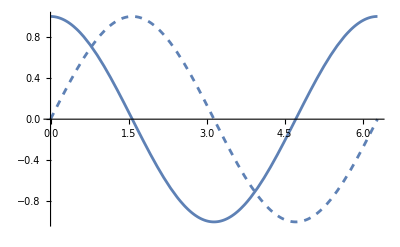

```mathematica
pic1=Plot[Sin[x],{x,0,2Pi},PlotStyle->Dashed];
pic2=Plot[Cos[x],{x,0,2π}];
Show[pic1,pic2]
```

```mathematica
变量替换
{
表达式/.规则表;
ClearAll;
a=x+y;b=x^2+y;
t=a^2+b^2;
t/.{x->1,y->1}(*规则表*)
}
```

变量替换

ReplaceAll::reps: {规则表} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

{8}

```mathematica
表达式
{
ClearAll;
t=x+2 x^2+3 x^3;
Print[t[[3]]];(*表达式的第三个元素*)
Print[t[[3,2]]](*表达式第三个元素的第二个元素*)
}
```

表达式

3 x^3

x^3

```mathematica
{
(*查询各种Form*)(*出于各种原因，这命令得你自己重打一次*)
CForm[Sin[x]];
TeXForm[Integrate[x^2Exp[x],x]](*这什么格式，没听过*);
Clear[a,b];
Print[a<b];
a=1;b=2;
Print[a<b];(*mathematica中包含TRUE FALSE 和无法确定三种情况，无法确定即输出原式子*)
Print[x^2+2 x+1!=(x+1)^2];(*该式子由于形式不同，无法判定*)
Print[Simplify[x^2+2 x+1!=(x+1)^2]]
}
```

a<b

True

1+2 x+x^2≠(1+x)^2

False

{Null}